# Synchronizing Metronomes (Entrainment)

## Analytic and Numerical Treatment

Ethan Knox

## Analytical Treatment

### Hanging Pendula on a Moving Platform

```mathematica
n:=2
vars:=Flatten[{x0[t],Table[q[i][t],{i,1,n}]}]
```

δw=w/(n-1)

```mathematica
dw:=w/(n-1)
```

x_i(t)=x_0(t)+(i-1) δw+l_i sin(q_i(t))
y_i(t)=-l_i cos(q_i(t))

```mathematica
x[i_][t_]:=x0[t]+(i-1) dw+l[i] Sin[q[i][t]]
y[i_][t_]:=-l[i] Cos[q[i][t]]
```

v_i(t)=√(((ẋ)_i)^2+((ẏ)_i)^2)→ v_i^2=((ẋ)_i)^2+((ẏ)_i)^2

```mathematica
v2[i_][t_]:=(x[i]'[t])^2+(y[i]'[t])^2
```

T=1/2 M((ẋ)_0)^2+(∑^n)_(i=1)1/2 m_i(v_i^2+α_i l_i^2((q̇)_i)^2)
V=(∑^n)_(i=1)m_i gy_i

```mathematica
T[t_]:=M/2 (x0'[t])^2+Sum[m[i]/2 (v2[i][t]+α[i] l[i]^2 (q[i]'[t])^2),{i,1,n}]
V[t_]:=Sum[m[i] g y[i][t],{i,1,n}]
```

L=T-V

```mathematica
L[t_]:=T[t]-V[t]
```

```mathematica
Needs["VariationalMethods`"]
ode=EulerEquations[L[t],vars,t]
(*solvedsoln:=First[Solve[soln,Flatten[{x0''[t],Table[q[i]''[t],{i,1,n}]}]]]*)
```

{-M x0''[t]-m[1] (-l[1] Sin[q[1][t]] (q[1]'[t])^2+x0''[t]+Cos[q[1][t]] l[1] q[1]''[t])-m[2] (-l[2] Sin[q[2][t]] (q[2]'[t])^2+x0''[t]+Cos[q[2][t]] l[2] q[2]''[t])==0,-l[1] m[1] (g Sin[q[1][t]]+Cos[q[1][t]] x0''[t]+l[1] (1+α[1]) q[1]''[t])==0,-l[2] m[2] (g Sin[q[2][t]]+Cos[q[2][t]] x0''[t]+l[2] (1+α[2]) q[2]''[t])==0}

## Numerical Treatment

### Enter subsection title here

#### Enter subsubsection title here

Enter text here. Enter TraditionalForm input for evaluation in a separate cell below:

```mathematica
α[1]=1/3;α[2]=1/3;
l[1]=1;l[2]=1;
m[1]=1;m[2]=1;
M=10;w=1;
g=9.81;
(*
ode={-x''[t]-(-Sin[θ[t]] θ'[t]^2+x''[t]+Cos[θ[t]] θ''[t])-(- Sin[ϕ[t]] ϕ'[t]^2+x''[t]+Cos[ϕ[t]] ϕ''[t])==0,-(Sin[θ[t]]+Cos[θ[t]] x''[t]+(1+1) θ''[t])==0,-(Sin[ϕ[t]]+Cos[ϕ[t]] x''[t]+(1+1) ϕ''[t])==0};
*)
ics={q[1]'[0]==0,q[2]'[0]==0,x0'[0]==0,q[1][0]==π/8+π/16,q[2][0]==π/8,x0[0]==0};
ode
```

{Sin[q[1][t]] (q[1]'[t])^2+Sin[q[2][t]] (q[2]'[t])^2-12 x0''[t]-Cos[q[1][t]] q[1]''[t]-Cos[q[2][t]] q[2]''[t]==0,-9.81 Sin[q[1][t]]-Cos[q[1][t]] x0''[t]-4/3 q[1]''[t]==0,-9.81 Sin[q[2][t]]-Cos[q[2][t]] x0''[t]-4/3 q[2]''[t]==0}

100

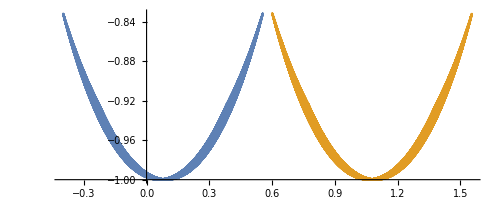

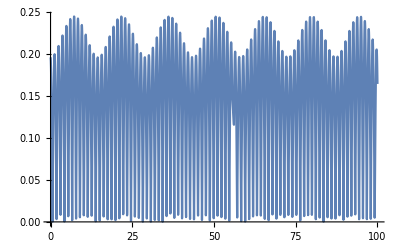

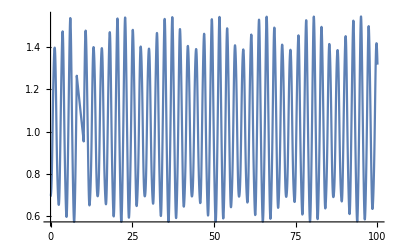

```mathematica
time=100
sol=First[NDSolve[Flatten[{ode,ics}],vars,{t,0,time}]];
x0[t_]:=Evaluate[x0[t]/.sol]
x1[t_]:=Evaluate[(x0[t]+Sin[q[1][t]])/.sol]
x2[t_]:=Evaluate[(x0[t]+(2-1)+Sin[q[2][t]])/.sol]
y1[t_]:=Evaluate[-Cos[q[1][t]]/.sol]
y2[t_]:=Evaluate[-Cos[q[2][t]]/.sol]

ParametricPlot[{{x1[t],y1[t]},{x2[t],y2[t]}},{t,0,time}]
Plot[(Abs[q[1][t]-q[2][t]])/.sol,{t,0,time}]
Plot[((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)/.sol,{t,0,time}]
```

```mathematica
frames=Table[Graphics[{Gray,Thick,Line[{{x0[t],0},{x1[t],y1[t]}}],Line[{{x0[t]+1,0},{x2[t],y2[t]}}],Darker[Red],Rectangle[{x0[t],0},{x0[t]+w,0.25}],Darker[Blue],Disk[{x1[t],y1[t]},.1],Disk[{x2[t],y2[t]},.1]},PlotRange->{{-1.5,3.},{-2.5,2.5}}],{t,0,time,.1}];
ListAnimate[frames]
```

Enter bulleted item text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter an inline formula like this: 2+2.

Enter numbered item text here.

Enter item paragraph text here.

Enter numbered subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for numbered display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter Wolfram Language program code below.

```mathematica
fun[x_]:=1
```

Enter text here. Enter non-Wolfram Language program code below.

DLLEXPORT int fun(WolframLibraryData libData, mreal A1, mreal *Res)
{
 mreal R0_0;
 mreal R0_1;
 R0_0 = A1;
 R0_1 = R0_0 * R0_0;
 *Res = R0_1;
 funStructCompile->WolframLibraryData_cleanUp(libData, 1);
 return 0;
}